```mathematica
generalSample = {-1.131202167003928,-0.1455046636163928,0.2483771681407099,0.08556467234959393,-1.6102125574072332,0.7399082129789132,1.7184545855730728,0.7096473402912746,-0.7491811264938547,0.13197015648991012,-0.9446630925936551,0.5786512672955654,1.5024373734734087,-1.6362058504826071,0.26723972907276744,0.3023142439590845,-0.925307067701843,-1.6094054628010508,-0.2493229705579086,0.21239046980004206,0.24976017400100908,-1.2800943491945065,1.2264074542913355,-0.5254785292916617,0.20073627574236844,2.3192084785233273,-0.53233268568186,-1.3393013785376369,-0.9965695555395108,-0.045381874270845425,1.498821997415805,-0.05852450904292314,0.6979639396637218,0.4744474014860127,-0.6604001849207844,-0.059694422123398094,-1.2579830982684606,1.4484150646685428,-0.22208082814368796,-1.1741961287641356,-0.04731525508840948,0.2122695328596178,-0.6861901181884424,1.039139276347656,-1.332733144152154,-0.505839971390325,-1.7392908595367598,1.409856149262908,1.2926627015776913,-1.579857213223825,-2.5968843943101807,-0.2211620104430586,-0.039055255021858325,0.1461762332440431,1.001558792721861,-0.2469465291049468,0.010783004650366782,-0.36702700662291166,-0.10103816024655402,-0.7338356791265684,0.679782027327071,-0.19276030223155838,-0.26303948678767314,-1.5922394516048723,0.8755608177160382,2.0285307499271608,0.9764944756314701,-0.4652487363187605,-2.4206834464944507,0.6991878471595522,-0.699877738337356,-0.9596488366877014,-1.4890209911245282,1.5625098001523,-2.076283470053153,-0.5891127057148948,0.43985606126116483,-0.9580411008524284,-0.6683951723738887,0.2729121363296493,0.036321458944979026,2.6765210435497084,-1.2185218587961881,0.574974765637273,1.0777037888087726,-1.8671995217732364,0.9277195702976793,0.9967505380183495,-0.9298675606643999,-0.24243710963031623,0.6654552823598386,2.390326890557364,-0.45860707343450363,-0.7222337022105767,-1.3962061614315604,0.05543741510716838,0.883003273335603,-0.6858002506021635,0.20638481278629706,-0.46061958630550365};
sortedSample = Sort[generalSample];
(*Grid[{Table[i, {i, 1, 20}], Map[Round[#,.001]&,sortedSample[[1;;20]]], Map[Round[#^2, .001]&,sortedSample[[1;;20]]], Table[i, {i, 21, 40}], Map[Round[#,.001]&,sortedSample[[21;;40]]], Map[Round[#^2, .001]&,sortedSample[[21;;40]]],Table[i, {i, 41, 60}], Map[Round[#,.001]&,sortedSample[[41;;60]]], Map[Round[#^2, .001]&,sortedSample[[41;;60]]], Table[i, {i, 61, 80}], Map[Round[#,.001]&,sortedSample[[61;;80]]], Map[Round[#^2, .001]&,sortedSample[[61;;80]]], Table[i, {i, 81,100}], Map[Round[#,.001]&,sortedSample[[81;;100]]], Map[Round[#^2, .001]&,sortedSample[[81;;100]]]} //Transpose, Frame->All]*)
Grid[{Table[i, {i, 1, 20}],  Map[Round[#, .001]&,generalSample[[1;;20]]],
Table[i, {i, 21, 40}],  Map[Round[#, .001]&,generalSample[[21;;40]]],
Table[i, {i, 41, 60}],  Map[Round[#, .001]&,generalSample[[41;;60]]],
Table[i, {i, 61, 80}],  Map[Round[#, .001]&,generalSample[[61;;80]]],
Table[i, {i, 81, 100}],  Map[Round[#, .001]&,generalSample[[81;;100]]]} //Transpose, Frame->All]
```

1 | -1.131 | 21 | 0.25 | 41 | -0.047 | 61 | 0.68 | 81 | 0.036
2 | -0.146 | 22 | -1.28 | 42 | 0.212 | 62 | -0.193 | 82 | 2.677
3 | 0.248 | 23 | 1.226 | 43 | -0.686 | 63 | -0.263 | 83 | -1.219
4 | 0.086 | 24 | -0.525 | 44 | 1.039 | 64 | -1.592 | 84 | 0.575
5 | -1.61 | 25 | 0.201 | 45 | -1.333 | 65 | 0.876 | 85 | 1.078
6 | 0.74 | 26 | 2.319 | 46 | -0.506 | 66 | 2.029 | 86 | -1.867
7 | 1.718 | 27 | -0.532 | 47 | -1.739 | 67 | 0.976 | 87 | 0.928
8 | 0.71 | 28 | -1.339 | 48 | 1.41 | 68 | -0.465 | 88 | 0.997
9 | -0.749 | 29 | -0.997 | 49 | 1.293 | 69 | -2.421 | 89 | -0.93
10 | 0.132 | 30 | -0.045 | 50 | -1.58 | 70 | 0.699 | 90 | -0.242
11 | -0.945 | 31 | 1.499 | 51 | -2.597 | 71 | -0.7 | 91 | 0.665
12 | 0.579 | 32 | -0.059 | 52 | -0.221 | 72 | -0.96 | 92 | 2.39
13 | 1.502 | 33 | 0.698 | 53 | -0.039 | 73 | -1.489 | 93 | -0.459
14 | -1.636 | 34 | 0.474 | 54 | 0.146 | 74 | 1.563 | 94 | -0.722
15 | 0.267 | 35 | -0.66 | 55 | 1.002 | 75 | -2.076 | 95 | -1.396
16 | 0.302 | 36 | -0.06 | 56 | -0.247 | 76 | -0.589 | 96 | 0.055
17 | -0.925 | 37 | -1.258 | 57 | 0.011 | 77 | 0.44 | 97 | 0.883
18 | -1.609 | 38 | 1.448 | 58 | -0.367 | 78 | -0.958 | 98 | -0.686
19 | -0.249 | 39 | -0.222 | 59 | -0.101 | 79 | -0.668 | 99 | 0.206
20 | 0.212 | 40 | -1.174 | 60 | -0.734 | 80 | 0.273 | 100 | -0.461

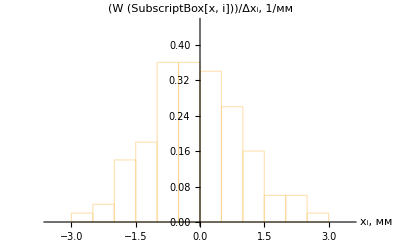

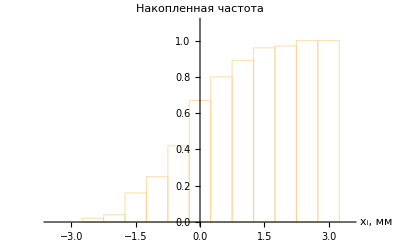

```mathematica
Show[ListPlot[{{-2.75, 0.01}, {-2.25, 0.02}, {-1.75, 0.07}, {-1.25, 0.08}, {-0.75, 0.18}, {-0.25, 0.18}, {0.25, 0.17}, {0.75, 0.13}, {1.25, 0.08}, {1.75, 0.03}, {2.25, 0.03}, {2.75, 0.01}}, BaseStyle->{FontFamily->"Cambria", FontSize->12, FontSlant->Italic}, AxesStyle->Arrowheads[{0, 0.03}], PlotRange->{{-3.5, 3.5}, {0, 0.23}}, AxesLabel->{"x_i, мм","W(x_i)"}, PlotStyle->Gray, Mesh->Full, Filling->Axis], ListLinePlot[{{-2.75, 0.01}, {-2.25, 0.02}, {-1.75, 0.07}, {-1.25, 0.08}, {-0.75, 0.18}, {-0.25, 0.18}, {0.25, 0.17}, {0.75, 0.13}, {1.25, 0.08}, {1.75, 0.03}, {2.25, 0.03}, {2.75, 0.01}}, BaseStyle->{FontFamily->"Cambria", FontSize->12, FontSlant->Italic}, AxesStyle->Arrowheads[{0, 0.03}], PlotRange->{{-3.5, 3.5}, {0, 0.23}}, AxesLabel->{"x_i, мм","W(x_i)"}, PlotStyle->Gray]];
Histogram[generalSample, {{-3, -2.5, -2, -1.5, -1, -0.5, 0, 0.5, 1, 1.5, 2, 2.5, 3}}, "PDF", BaseStyle->{FontFamily->"Cambria", FontSize->12, FontSlant->Italic}, ChartStyle->{White}, AxesStyle->Arrowheads[{0, 0.03}], PlotRange->{{-3.5, 3.5}, {0, 0.45}}, AxesOrigin->{0, 0},AxesLabel->{"x_i, мм","(W (SubscriptBox[x, i]))/Δx_i, 1/(:043c:043c)"}]
Histogram[generalSample, {{-2.75, -2.25, -1.75, -1.25, -0.75, -0.25, 0.25, 0.75, 1.25, 1.75, 2.25, 2.75, 3.25}}, "CDF", BaseStyle->{FontFamily->"Cambria", FontSize->12, FontSlant->Italic}, ChartStyle->{White}, AxesStyle->Arrowheads[{0, 0.03}], PlotRange->{{-3.5, 3.5}, {0, 1.1}}, AxesOrigin->{0, 0},AxesLabel->{"x_i, мм","Накопленная частота"}]
```

```mathematica
(2.75^2+2*2.25^2+7*1.75^2+8*1.25^2+18*0.75^2+18*0.25^2+17*0.25^2+13*0.75^2+8*1.25^2+3*1.75^2+3*2.25^2+1*2.75^2)/100-0.0875^2
Sqrt[%]
midIntervals=Table[i*0.5-2.75, {i, 0, 11}]
relMidIntervals=Map[(#+0.25)/0.5&,midIntervals];
freqs={1, 2, 7, 9, 18, 18, 17, 13, 8, 3, 3, 1};
Grid[{Table[i, {i, 1, 12}], midIntervals, relMidIntervals, relMidIntervals^2, relMidIntervals^3, relMidIntervals^4,freqs, relMidIntervals*freqs, freqs*relMidIntervals^2, freqs*relMidIntervals^3, freqs*relMidIntervals^4}//Transpose, Frame->All]
Total[freqs]
```

1.14922

1.07202

{-2.75,-2.25,-1.75,-1.25,-0.75,-0.25,0.25,0.75,1.25,1.75,2.25,2.75}

1 | -2.75 | -5. | 25. | -125. | 625. | 1 | -5. | 25. | -125. | 625.
2 | -2.25 | -4. | 16. | -64. | 256. | 2 | -8. | 32. | -128. | 512.
3 | -1.75 | -3. | 9. | -27. | 81. | 7 | -21. | 63. | -189. | 567.
4 | -1.25 | -2. | 4. | -8. | 16. | 9 | -18. | 36. | -72. | 144.
5 | -0.75 | -1. | 1. | -1. | 1. | 18 | -18. | 18. | -18. | 18.
6 | -0.25 | 0. | 0. | 0. | 0. | 18 | 0. | 0. | 0. | 0.
7 | 0.25 | 1. | 1. | 1. | 1. | 17 | 17. | 17. | 17. | 17.
8 | 0.75 | 2. | 4. | 8. | 16. | 13 | 26. | 52. | 104. | 208.
9 | 1.25 | 3. | 9. | 27. | 81. | 8 | 24. | 72. | 216. | 648.
10 | 1.75 | 4. | 16. | 64. | 256. | 3 | 12. | 48. | 192. | 768.
11 | 2.25 | 5. | 25. | 125. | 625. | 3 | 15. | 75. | 375. | 1875.
12 | 2.75 | 6. | 36. | 216. | 1296. | 1 | 6. | 36. | 216. | 1296.

100

```mathematica
BinCounts[generalSample,{-3,3,0.5}]
```

{1,2,7,9,18,18,17,13,8,3,3,1}

```mathematica
f[y_]:=1/Sqrt[2*Pi] Integrate[Exp[-t^2/2], {t, 0, y}]
f[-2.54]
```

-0.494457

```mathematica
Solve[{(-0.459-m)/s==-0.26, (0.132-m)/s==0.26}, {m, s}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{m→-0.1635,s→1.13654}}

```mathematica
Total[generalSample[[1;;20]]^2]/20-Mean[generalSample[[1;;20]]]^2;
f[({-2.5, -2.0, -1.5, -1.0, -0.5, 0, 0.5, 1.0, 1.5, 2.0, 2.5}+0.1)/1.078]
```

{-0.487004,-0.46101,-0.402977,-0.298107,-0.144703,0.0369546,0.211095,0.346233,0.431126,0.474296,0.492065}

```mathematica
100*{0.008,0.018,0.043,0.085,0.135,0.174,0.182,0.153,0.105,0.058,0.026,0.013}
```

{0.8,1.8,4.3,8.5,13.5,17.4,18.2,15.3,10.5,5.8,2.6,1.3}

```mathematica
MapIndexed[{Subscript[x, First[#2]], #1}&,generalSample[[1;;20]]]
MapIndexed[{Subscript[y, First[#2]], #1}&,generalSample[[81;;100]]]
Join[%%,%]
SortBy[%, Last]
```

{{x_1,-1.1312},{x_2,-0.145505},{x_3,0.248377},{x_4,0.0855647},{x_5,-1.61021},{x_6,0.739908},{x_7,1.71845},{x_8,0.709647},{x_9,-0.749181},{x_10,0.13197},{x_11,-0.944663},{x_12,0.578651},{x_13,1.50244},{x_14,-1.63621},{x_15,0.26724},{x_16,0.302314},{x_17,-0.925307},{x_18,-1.60941},{x_19,-0.249323},{x_20,0.21239}}

{{y_1,0.0363215},{y_2,2.67652},{y_3,-1.21852},{y_4,0.574975},{y_5,1.0777},{y_6,-1.8672},{y_7,0.92772},{y_8,0.996751},{y_9,-0.929868},{y_10,-0.242437},{y_11,0.665455},{y_12,2.39033},{y_13,-0.458607},{y_14,-0.722234},{y_15,-1.39621},{y_16,0.0554374},{y_17,0.883003},{y_18,-0.6858},{y_19,0.206385},{y_20,-0.46062}}

{{x_1,-1.1312},{x_2,-0.145505},{x_3,0.248377},{x_4,0.0855647},{x_5,-1.61021},{x_6,0.739908},{x_7,1.71845},{x_8,0.709647},{x_9,-0.749181},{x_10,0.13197},{x_11,-0.944663},{x_12,0.578651},{x_13,1.50244},{x_14,-1.63621},{x_15,0.26724},{x_16,0.302314},{x_17,-0.925307},{x_18,-1.60941},{x_19,-0.249323},{x_20,0.21239},{y_1,0.0363215},{y_2,2.67652},{y_3,-1.21852},{y_4,0.574975},{y_5,1.0777},{y_6,-1.8672},{y_7,0.92772},{y_8,0.996751},{y_9,-0.929868},{y_10,-0.242437},{y_11,0.665455},{y_12,2.39033},{y_13,-0.458607},{y_14,-0.722234},{y_15,-1.39621},{y_16,0.0554374},{y_17,0.883003},{y_18,-0.6858},{y_19,0.206385},{y_20,-0.46062}}

{{y_6,-1.8672},{x_14,-1.63621},{x_5,-1.61021},{x_18,-1.60941},{y_15,-1.39621},{y_3,-1.21852},{x_1,-1.1312},{x_11,-0.944663},{y_9,-0.929868},{x_17,-0.925307},{x_9,-0.749181},{y_14,-0.722234},{y_18,-0.6858},{y_20,-0.46062},{y_13,-0.458607},{x_19,-0.249323},{y_10,-0.242437},{x_2,-0.145505},{y_1,0.0363215},{y_16,0.0554374},{x_4,0.0855647},{x_10,0.13197},{y_19,0.206385},{x_20,0.21239},{x_3,0.248377},{x_15,0.26724},{x_16,0.302314},{y_4,0.574975},{x_12,0.578651},{y_11,0.665455},{x_8,0.709647},{x_6,0.739908},{y_17,0.883003},{y_7,0.92772},{y_8,0.996751},{y_5,1.0777},{x_13,1.50244},{x_7,1.71845},{y_12,2.39033},{y_2,2.67652}}

```mathematica
3+9+11+11+1+14+17+14+4+11+3+13+18+1+12+12+4+1+8+12
```

179